# Non Gaussian

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{1,1,1,1,1,1,1,1,2500,2500,3000,7000,10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 999999 ,999999}};
```

```mathematica
tauAlphas2DVoro={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3},{1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4}}[[;;,;;,1]];
```

```mathematica
tauAlphas2DVoro={{1.1833045281591739,5.598944530254805,8.869681254159824,23.06915604814413,33.47216517177899,52.13604938957775,70.26110474336024,184.8389219330216,469.9966551958508,928.9141411257335,1388.8573388558757,3733.7965726246803,7188.0211906943905,9930.440141161429,20363.412050391147,28926.20974169952,40853.651332495545},{0.7900326516170211,2.289574011305053,2.958250485864885,8.175170221727768,18.62429236287473,26.7057065030922,38.93262330160253,53.82663082998007,85.98952898577276,116.96119749155234,170.26910629468244,249.98760192489448,477.78558515293264,1165.8293615058974,4460.353833504053,13046.252906883372},{0.8123588919200075,2.764809517861429,3.926947303972556,5.5322457986348414,13.32673763266526,38.707004602866355,61.57546102366048,113.70161623865071,225.11065798439728,550.157473723199,1423.1126638068067,2571.701791242669,4591.206662582439,8306.584752444407},{4.6928697345434385,7.154118682571008,12.908598892568973,23.322858837870957,63.67532549552178,134.46736178733312,215.05026318914835,530.794939576096,742.093995695809,1380.4983136647434,2856.371850023293,7227.75083967605,8665.801909860707},{1.9262900500995055,4.287542146945071,8.229903335418154,13.323420575172946,25.461272313291317,65.05251101056447,175.20637182592745,622.3030392633742,1311.405074775784,4715.68147756796,10694.488268838475}};
```

```mathematica
trueCRMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueCRMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMSD_N4096_p3.7750_T0.02500000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMSD_N4096_p3.7750_T0.01600000_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMSD_N4096_p3.7750_T0.00560000_waitingTime70000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
trueCRMFDs=Table[Table[
DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueCRMFD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMFD_N4096_p3.7750_T0.02500000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMFD_N4096_p3.7750_T0.01600000_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.775/timeTrueCRMFD_N4096_p3.7750_T0.00560000_waitingTime70000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
meanCRMFD=Table[Table[Table[{trueCRMFDs[[p,T,1,1,rec]],Mean[Table[If[Length[trueCRMSDs[[p,T,i,2]]]<=150/110*Min[Table[Length[trueCRMSDs[[p,T,i,2]]],{i,Length[trueCRMSDs[[p,T]]]}]],trueCRMFDs[[p,T,i,2,rec]],Nothing],{i,Length[trueCRMFDs[[p,T]]]}]]},{rec,Min[Table[Length[trueCRMFDs[[p,T,i,2]]],{i,Length[trueCRMFDs[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
meanCRMSD=Table[Table[Table[{trueCRMSDs[[p,T,1,1,rec]],Mean[Table[If[Length[trueCRMSDs[[p,T,i,2]]]<=150/110*Min[Table[Length[trueCRMSDs[[p,T,i,2]]],{i,Length[trueCRMSDs[[p,T]]]}]],trueCRMSDs[[p,T,i,2,rec]],Nothing],{i,Length[trueCRMSDs[[p,T]]]}]]},{rec,Min[Table[Length[trueCRMSDs[[p,T,i,2]]],{i,Length[trueCRMSDs[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
trueCRMSDs[[3,2]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
Normal[trueCRMSDs[[3,-1,1,1]]]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.54,0.55,0.56,0.58,0.59,0.6,0.62,0.63,0.65,0.66,0.68,0.69,0.71,0.72,0.74,0.76,0.78,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.98,1.,1.02,1.05,1.07,1.1,1.12,1.15,1.17,1.2,1.23,1.26,1.29,1.32,1.35,1.38,1.41,1.45,1.48,1.51,1.55,1.58,1.62,1.66,1.7,1.74,1.78,1.82,1.86,1.91,1.95,2.,2.04,2.09,2.14,2.19,2.24,2.29,2.34,2.4,2.45,2.51,2.57,2.63,2.69,2.75,2.82,2.88,2.95,3.02,3.09,3.16,3.24,3.31,3.39,3.47,3.55,3.63,3.72,3.8,3.89,3.98,4.07,4.17,4.27,4.37,4.47,4.57,4.68,4.79,4.9,5.01,5.13,5.25,5.37,5.5,5.62,5.75,5.89,6.03,6.17,6.31,6.46,6.61,6.76,6.92,7.08,7.24,7.41,7.59,7.76,7.94,8.13,8.32,8.51,8.71,8.91,9.12,9.33,9.55,9.77,10.,10.23,10.47,10.72,10.96,11.22,11.48,11.75,12.02,12.3,12.59,12.88,13.18,13.49,13.8,14.13,14.45,14.79,15.14,15.49,15.85,16.22,16.6,16.98,17.38,17.78,18.2,18.62,19.05,19.5,19.95,20.42,20.89,21.38,21.88,22.39,22.91,23.44,23.99,24.55,25.12,25.7,26.3,26.92,27.54,28.18,28.84,29.51,30.2,30.9,31.62,32.36,33.11,33.88,34.67,35.48,36.31,37.15,38.02,38.9,39.81,40.74,41.69,42.66,43.65,44.67,45.71,46.77,47.86,48.98,50.12,51.29,52.48,53.7,54.95,56.23,57.54,58.88,60.26,61.66,63.1,64.57,66.07,67.61,69.18,70.79,72.44,74.13,75.86,77.62,79.43,81.28,83.18,85.11,87.1,89.13,91.2,93.33,95.5,97.72,100.,102.33,104.71,107.15,109.65,112.2,114.82,117.49,120.23,123.03,125.89,128.82,131.83,134.9,138.04,141.25,144.54,147.91,151.36,154.88,158.49,162.18,165.96,169.82,173.78,177.83,181.97,186.21,190.55,194.98,199.53,204.17,208.93,213.8,218.78,223.87,229.09,234.42,239.88,245.47,251.19,257.04,263.03,269.15,275.42,281.84,288.4,295.12,302.,309.03,316.23,323.59,331.13,338.84,346.74,354.81,363.08,371.54,380.19,389.05,398.11,407.38,416.87,426.58,436.52,446.68,457.09,467.74,478.63,489.78,501.19,512.86,524.81,537.03,549.54,562.34,575.44,588.84,602.56,616.6,630.96,645.65,660.69,676.08,691.83,707.95,724.44,741.31,758.58,776.25,794.33,812.83,831.76,851.14,870.96,891.25,912.01,933.25,954.99,977.24,1000.,1023.29,1047.13,1071.52,1096.48,1122.02,1148.15,1174.9,1202.26,1230.27,1258.93,1288.25,1318.26,1348.96,1380.38,1412.54,1445.44,1479.11,1513.56,1548.82,1584.89,1621.81,1659.59,1698.24,1737.8,1778.28,1819.7,1862.09,1905.46,1949.84,1995.26,2041.74,2089.3,2137.96,2187.76,2238.72,2290.87,2344.23,2398.83,2454.71,2511.89,2570.4,2630.27,2691.53,2754.23,2818.38,2884.03,2951.21,3019.95,3090.3,3162.28,3235.94,3311.31,3388.44,3467.37,3548.13,3630.78,3715.35,3801.89,3890.45,3981.07,4073.8,4168.69,4265.8,4365.16,4466.84,4570.88,4677.35,4786.3,4897.79,5011.87,5128.61,5248.07,5370.32,5495.41,5623.41,5754.4,5888.44,6025.6,6165.95,6309.57,6456.54,6606.93,6760.83,6918.31,7079.46,7244.36,7413.1,7585.78,7762.47,7943.28,8128.31,8317.64,8511.38,8709.64,8912.51,9120.11,9332.54,9549.93,9772.37,10000.,10232.9,10471.3,10715.2,10964.8,11220.2,11481.5,11749.,12022.6,12302.7,12589.3,12882.5,13182.6,13489.6,13803.8,14125.4,14454.4,14791.1,15135.6,15488.2,15848.9,16218.1,16595.9,16982.4,17378.,17782.8,18197.,18620.9,19054.6,19498.5,19952.6,20417.4,20893.,21379.6,21877.6,22387.2,22908.7,23442.3,23988.3,24547.1,25118.9,25704.,26302.7,26915.4,27542.3,28183.8,28840.3,29512.1,30199.5,30903.,31622.8,32359.4,33113.1,33884.4,34673.7,35481.3,36307.8,37153.5,38018.9,38904.5,39810.7,40738.,41686.9,42658.,43651.6,44668.4,45708.8,46773.5,47863.,48977.9,50118.7,51286.1,52480.8,53703.2,54954.1,56234.1,57544.,58884.4,60256.,61659.5,63095.7,64565.4,66069.3,67608.3,69183.1,70794.6,72443.6,74131.,75857.8,77624.7,79432.8,81283.1,83176.4,85113.8,87096.4,89125.1,91201.1,93325.4,95499.3,97723.7,100000.,102329.,104713.,107152.,109648.,112202.,114815.,117490.,120226.,123027.,125893.,128825.,131826.,134896.,138038.,141254.,144544.,147911.,151356.,154882.,158489.,162181.,165959.,169824.,173780.,177828.,181970.,186209.,190546.,194984.,199526.,204174.,208930.,213796.,218776.,223872.,229087.,234423.,239883.,245471.,251189.,257040.,263027.,269153.,275423.,281838.,288403.,295121.,301995.,309030.,316228.,323594.,331131.,338844.,346737.,354813.,363078.,371535.,380189.,389045.,398107.}

```mathematica
Normal[trueCRMSDs[[3,-1,2,1]]]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.54,0.55,0.56,0.58,0.59,0.6,0.62,0.63,0.65,0.66,0.68,0.69,0.71,0.72,0.74,0.76,0.78,0.79,0.81,0.83,0.85,0.87,0.89,0.91,0.93,0.95,0.98,1.,1.02,1.05,1.07,1.1,1.12,1.15,1.17,1.2,1.23,1.26,1.29,1.32,1.35,1.38,1.41,1.45,1.48,1.51,1.55,1.58,1.62,1.66,1.7,1.74,1.78,1.82,1.86,1.91,1.95,2.,2.04,2.09,2.14,2.19,2.24,2.29,2.34,2.4,2.45,2.51,2.57,2.63,2.69,2.75,2.82,2.88,2.95,3.02,3.09,3.16,3.24,3.31,3.39,3.47,3.55,3.63,3.72,3.8,3.89,3.98,4.07,4.17,4.27,4.37,4.47,4.57,4.68,4.79,4.9,5.01,5.13,5.25,5.37,5.5,5.62,5.75,5.89,6.03,6.17,6.31,6.46,6.61,6.76,6.92,7.08,7.24,7.41,7.59,7.76,7.94,8.13,8.32,8.51,8.71,8.91,9.12,9.33,9.55,9.77,10.,10.23,10.47,10.72,10.96,11.22,11.48,11.75,12.02,12.3,12.59,12.88,13.18,13.49,13.8,14.13,14.45,14.79,15.14,15.49,15.85,16.22,16.6,16.98,17.38,17.78,18.2,18.62,19.05,19.5,19.95,20.42,20.89,21.38,21.88,22.39,22.91,23.44,23.99,24.55,25.12,25.7,26.3,26.92,27.54,28.18,28.84,29.51,30.2,30.9,31.62,32.36,33.11,33.88,34.67,35.48,36.31,37.15,38.02,38.9,39.81,40.74,41.69,42.66,43.65,44.67,45.71,46.77,47.86,48.98,50.12,51.29,52.48,53.7,54.95,56.23,57.54,58.88,60.26,61.66,63.1,64.57,66.07,67.61,69.18,70.79,72.44,74.13,75.86,77.62,79.43,81.28,83.18,85.11,87.1,89.13,91.2,93.33,95.5,97.72,100.,102.33,104.71,107.15,109.65,112.2,114.82,117.49,120.23,123.03,125.89,128.82,131.83,134.9,138.04,141.25,144.54,147.91,151.36,154.88,158.49,162.18,165.96,169.82,173.78,177.83,181.97,186.21,190.55,194.98,199.53,204.17,208.93,213.8,218.78,223.87,229.09,234.42,239.88,245.47,251.19,257.04,263.03,269.15,275.42,281.84,288.4,295.12,302.,309.03,316.23,323.59,331.13,338.84,346.74,354.81,363.08,371.54,380.19,389.05,398.11,407.38,416.87,426.58,436.52,446.68,457.09,467.74,478.63,489.78,501.19,512.86,524.81,537.03,549.54,562.34,575.44,588.84,602.56,616.6,630.96,645.65,660.69,676.08,691.83,707.95,724.44,741.31,758.58,776.25,794.33,812.83,831.76,851.14,870.96,891.25,912.01,933.25,954.99,977.24,1000.,1023.29,1047.13,1071.52,1096.48,1122.02,1148.15,1174.9,1202.26,1230.27,1258.93,1288.25,1318.26,1348.96,1380.38,1412.54,1445.44,1479.11,1513.56,1548.82,1584.89,1621.81,1659.59,1698.24,1737.8,1778.28,1819.7,1862.09,1905.46,1949.84,1995.26,2041.74,2089.3,2137.96,2187.76,2238.72,2290.87,2344.23,2398.83,2454.71,2511.89,2570.4,2630.27,2691.53,2754.23,2818.38,2884.03,2951.21,3019.95,3090.3,3162.28,3235.94,3311.31,3388.44,3467.37,3548.13,3630.78,3715.35,3801.89,3890.45,3981.07,4073.8,4168.69,4265.8,4365.16,4466.84,4570.88,4677.35,4786.3,4897.79,5011.87,5128.61,5248.07,5370.32,5495.41,5623.41,5754.4,5888.44,6025.6,6165.95,6309.57,6456.54,6606.93,6760.83,6918.31,7079.46,7244.36,7413.1,7585.78,7762.47,7943.28,8128.31,8317.64,8511.38,8709.64,8912.51,9120.11,9332.54,9549.93,9772.37,10000.,10232.9,10471.3,10715.2,10964.8,11220.2,11481.5,11749.,12022.6,12302.7,12589.2,12882.5,13182.6,13489.6,13803.8,14125.4,14454.4,14791.1,15135.6,15488.2,15848.9,16218.1,16595.9,16982.4,17378.,17782.8,18197.,18620.9,19054.6,19498.4,19952.6,20417.4,20893.,21379.6,21877.6,22387.2,22908.7,23442.3,23988.3,24547.1,25118.9,25704.,26302.7,26915.3,27542.3,28183.8,28840.3,29512.1,30199.5,30902.9,31622.8,32359.4,33113.1,33884.4,34673.7,35481.3,36307.8,37153.5,38018.9,38904.5,39810.7,40738.,41686.9,42658.,43651.6,44668.4,45708.8,46773.5,47863.,48977.9,50118.7,51286.1,52480.8,53703.2,54954.1,56234.1,57544.,58884.4,60256.,61659.5,63095.7,64565.4,66069.3,67608.3,69183.1,70794.6,72443.6,74131.,75857.8,77624.7,79432.8,81283.1,83176.4,85113.8,87096.4,89125.1,91201.1,93325.4,95499.3,97723.7}

```mathematica
trueCRMFDs[[3,-1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

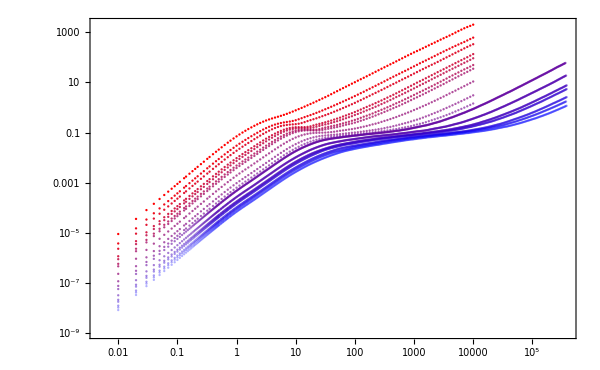
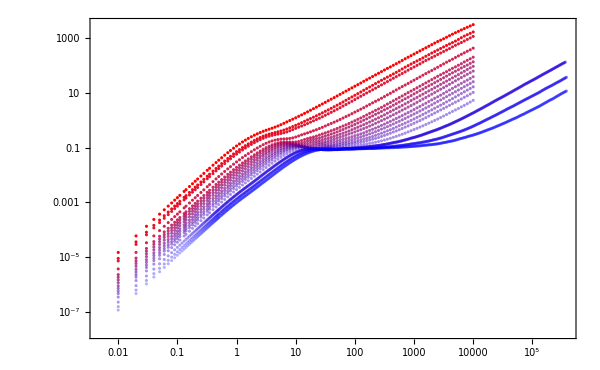
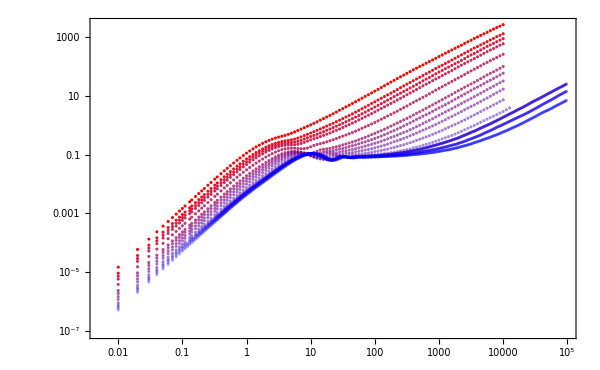
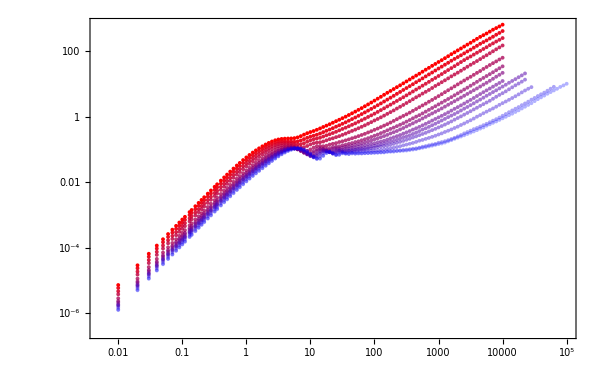
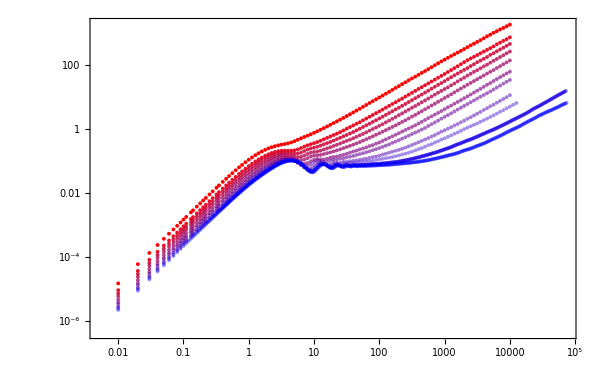

```mathematica
Table[ListLogLogPlot[meanCRMSD[[p]],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],ImageSize->600],{p,Length[p0s]}]
```

## Non gaussian

```mathematica
nonGaussian=Table[Table[Table[If[meanCRMSD[[p,T,t,2]]>=0.00001,meanCRMFD[[p,T,t,2]]/meanCRMSD[[p,T,t,2]]^2/2-1,0],{t,Length[meanCRMFD[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

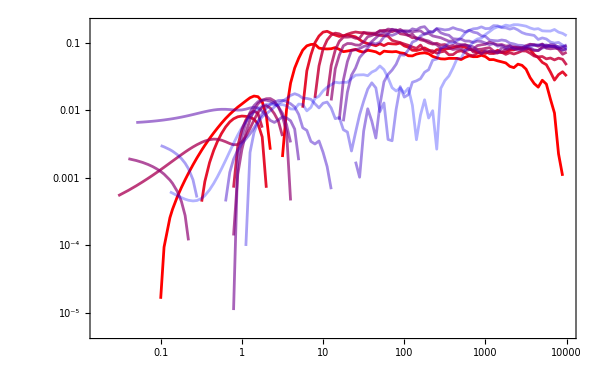
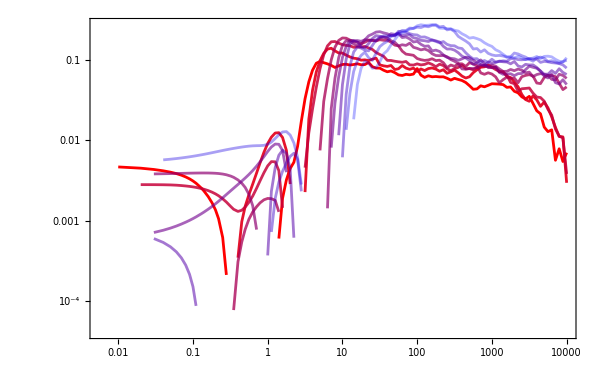
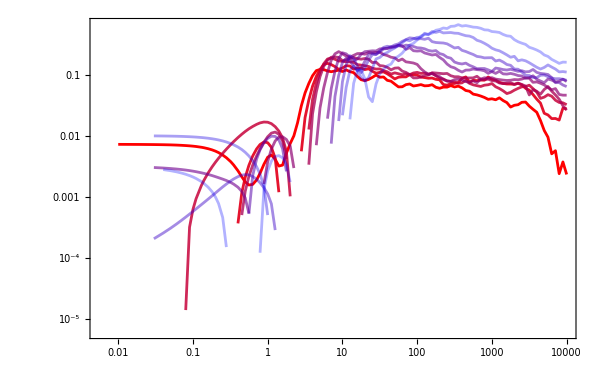
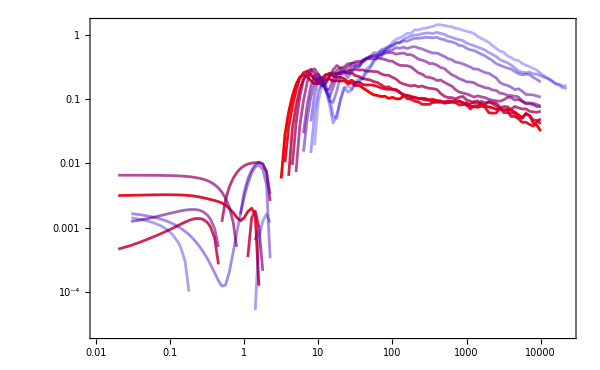
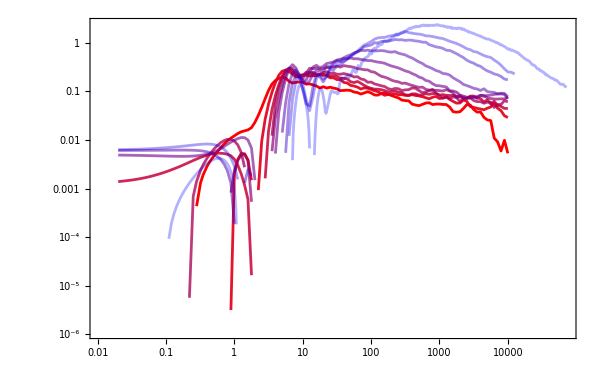

```mathematica
Table[ListLogLogPlot[Table[Table[{meanCRMSD[[p,T,t,1]],nonGaussian[[p,T,t]]},{t,Length[meanCRMFD[[p,T]]]}],{T,10}],PlotStyle->redBluePlotConfig[10],Joined->True,ImageSize->600],{p,1,5}]
```

```mathematica
Normal[trueCRMSDs[[3,4,6,1]]]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.2,0.22,0.23,0.25,0.27,0.29,0.32,0.34,0.37,0.4,0.43,0.46,0.5,0.54,0.58,0.63,0.68,0.74,0.79,0.86,0.93,1.,1.08,1.17,1.26,1.36,1.47,1.58,1.71,1.85,2.,2.15,2.33,2.51,2.71,2.93,3.16,3.41,3.69,3.98,4.3,4.64,5.01,5.41,5.84,6.31,6.81,7.36,7.94,8.58,9.26,10.,10.8,11.66,12.59,13.59,14.68,15.85,17.11,18.48,19.95,21.54,23.26,25.12,27.12,29.29,31.62,34.15,36.87,39.81,42.99,46.42,50.12,54.12,58.43,63.1,68.13,73.56,79.43,85.77,92.61,100.,107.98,116.59,125.89,135.94,146.78,158.49,171.13,184.78,199.53,215.44,232.63,251.19,271.23,292.86,316.23,341.45,368.69,398.11,429.87,464.16,501.19,541.17,584.34,630.96,681.29,735.64,794.33,857.7,926.12,1000.,1079.78,1165.91,1258.93,1359.36,1467.8,1584.89,1711.33,1847.85,1995.26,2154.43,2326.31,2511.89,2712.27,2928.64,3162.28,3414.55,3686.95,3981.07,4298.66,4641.59,5011.87,5411.7,5843.41,6309.57,6812.92,7356.42,7943.28,8576.96,9261.19,10000.}

```mathematica
Normal[trueCRMSDs[[3,4,1,1]]]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.}

```mathematica
Table[If[meanCRMFD[[3,1,t,1]]>=0.1,nonGaussian[[3,1,t]],Nothing],{t,Length[meanCRMFD[[3,1]]]}]
```

{0.00714863,0.00714285,0.0119023,0.0111823,0.0198731,0.0299162,0.0399187,0.0493095,0.070698,0.0725758,0.0843247,0.0990497,0.115067,0.127733,0.137841,0.140775,0.158029,0.166829,0.173338,0.184857,0.195944,0.198944,0.202373,0.204561,0.203439,0.205906,0.204359,0.206802,0.20672,0.216931,0.231708,0.246793,0.26393,0.281274,0.284756,0.284959,0.282873,0.283734,0.292008,0.30291,0.304143,0.320801,0.323341,0.331754,0.32748,0.326485,0.336203,0.353782,0.375774,0.400254,0.400741,0.411994,0.406304,0.410118,0.405739,0.402831,0.40921,0.422901,0.430706,0.429519,0.437201,0.445159,0.445359,0.450177,0.45731,0.451598,0.451743,0.458933,0.462156,0.469966,0.467971,0.473717,0.470314,0.46405,0.46387,0.457268,0.457215,0.455979,0.454129,0.451193,0.453889,0.453017,0.458398,0.453498,0.45054,0.443742,0.447399,0.449307,0.454671,0.455905,0.449392,0.445527,0.441876,0.433516,0.426185,0.422799,0.417337,0.418976,0.414917,0.41712,0.415624}

```mathematica
peakNonGau=Table[Table[Max[Table[If[meanCRMFD[[p,T,t,1]]>=10,nonGaussian[[p,T,t]],Nothing],{t,Length[meanCRMFD[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0853596,0.148814,0.145363,0.154881,0.160763,0.159523,0.17435,0.168581,0.180609,0.186721,0.197656,0.196915,0.194874,0.191217,0.187223,0.19929,0.215569},{0.0926893,0.121303,0.154329,0.187053,0.191577,0.223802,0.214235,0.226367,0.273304,0.273617,0.292511,0.309377,0.345482,0.458609,0.574567,0.723659},{0.120478,0.141526,0.166768,0.192907,0.235037,0.307508,0.307327,0.404666,0.517822,0.666329,0.8987,1.15185,1.25447,1.35466},{0.206606,0.243127,0.266261,0.292335,0.436546,0.530625,0.655301,0.915882,1.09292,1.44003,1.62558,2.05078,2.3488},{0.152151,0.224302,0.235156,0.252776,0.336743,0.485073,0.700247,1.16308,1.69095,2.34424,3.18693}}

```mathematica
meanCRMFD[[1,1,1,1]]
```

0.01